```mathematica
SymbolToKey[s_]:=FromDigits[StringDrop[SymbolName[s],1]]
```

```mathematica
RelationsToEdges[key_]:=Block[{current=newAssoc[key],rel2, result={}, lhs, rhs,one,two,three},
Table[
rel2=Simplify[rel];
lhs=rel2[[1]];
rhs=rel2[[2]];
If[Length[lhs]==0,
one=SymbolToKey[lhs];
two=SymbolToKey[rhs[[1]]];
three=SymbolToKey[rhs[[2]]];
,
one=SymbolToKey[rhs];
two=SymbolToKey[lhs[[1]]];
three=SymbolToKey[lhs[[2]]]
];
If[one==1&&(two==0||three==0),Print[{key,rel}]];
(*If[ToString[newAssoc[one]["comp"]]!=ToString[newAssoc[two]["comp"]],
result=Append[result,{one->two}];
];
If[ToString[newAssoc[one]["comp"]]!=ToString[newAssoc[three]["comp"]],
result=Append[result,{one->three}];
];*)
result=Append[result,{one->two,one->three}];
,{rel,current["relations"]}
];
Flatten[result]
]
```

```mathematica
Length[allDependencies]
```

14710

```mathematica
allDependencies =DeleteDuplicates[ Flatten[Table[RelationsToEdges[key],{key,Keys[newAssoc]}]]];Take[allDependencies,5]
```

{0→243,0→486,0→162,0→81,0→27}

```mathematica
vcolors=Table[k->If[ToString[newAssoc[k]["comp"]]=="Greater",If[KeyExistsQ[newAssoc[k],"compwhy"],Darker[Green],Green],If[ToString[newAssoc[k]["comp"]]=="GreaterEqual",Red,Blue]],{k,Keys[newAssoc]}];
```

```mathematica
demoValues={z->3728,b06->2520,b04->3000,b07->2488,b34->1280,b02->2852,b17->1940,b05->2852,b12->2324,b26->1292,b08->2348,b22->1590,b28->1268,b35->1108,b47->264,b10->2384,b21->1596,b20->1848,b24->1500,b40->712,b03->2616,b11->2120,b15->1996,b18->1682,b43->894,b33->1112,b38->702,b01->2640,b16->1772,b14->2038,b13->2050,b41->912,b30->1112,b45->870,b27->976,b42->746,b46->224,b09->2360,b25->1558,b19->1924,b23->1598,b39->796,b32->980,b37->672,b29->1060,b44->870,b50->230,b31->980,b36->628,b49->186,b48->182};
```

```mathematica
vsizes=Table[k->N[1/(1+(newAssoc[k]["colofour"]/.demoValues))],{k,Keys[newAssoc]}];Take[vsizes,5]
```

{0→0.000268168,1→0.000396668,2→0.00082713,3→0.000333222,4→0.000463607}

```mathematica
redLabels=Table[k->ToString[k],{k,Select[DeleteDuplicates[Flatten[Map[{#[[1]],#[[2]]}&,allDependencies]]],ToString[newAssoc[#]["comp"]]=="GreaterEqual"&]}];Length[redLabels]
```

4

```mathematica
vert=DepthFirstScan[Graph[allDependencies],0,{"PrevisitVertex"->(#&)}]//DeleteDuplicates;
```

```mathematica
depGraph=Graph[ allDependencies, VertexLabels->{29524->"K5",59048->"Dot"}, EdgeShapeFunction->GraphElementData[{"Line","ArrowSize"->.0}],
VertexStyle->vcolors,  ImageSize->800,GraphLayout->Automatic]
```

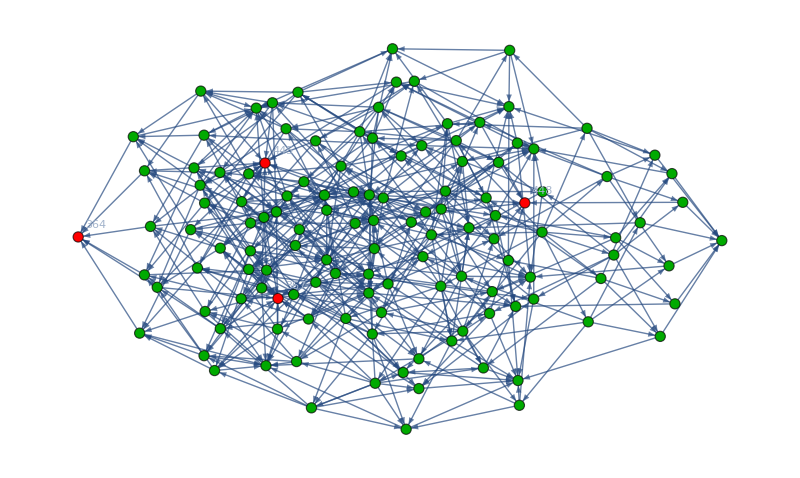

```mathematica
depGraph=Graph[ allDependencies,  VertexLabels->redLabels,VertexStyle->Select[vcolors,VertexQ[Graph[allDependencies],#[[1]]]&],
  ImageSize->800,EdgeStyle->Arrowheads[0.001]]
```

```mathematica
Table[CompGraph[key],{key,{29488,29515,29497}}]
```

{-Graphics-Greater29488,-Graphics-GreaterEqual29515,-Graphics-GreaterEqual29497}

```mathematica
Wave[start_,n_]:=Select[Keys[newAssoc],GraphDistance[depGraph,start,#]==n&]
```

```mathematica
WaveEnd[end_,n_]:=Select[Keys[newAssoc],GraphDistance[depGraph,#,end]==n&]
```

```mathematica
WaveEnd[364,1]
```

{121,283,337,355,361,363}

```mathematica
newAssoc[168]
```

<|signature→168,matrix→{{2,0,2,0},{0,2,0,2},{2,0,2,0},{0,2,0,2}},graph→-Graphics-,vertexsets→{{1,3},{2,4}},vertices→{1,2},edges→{},relations→{x168==x448+x728},links→{728,448},colofour→-v05-v06+v13+z,comp→Greater,compwhy→the relation holds : x168 == x448 + x728 and x728 has a strictly positive colofour,colofour2→-v05-v06+v13+z|>

```mathematica
Map[
With[{
g=newAssoc[#]["graph"],
c=ToString[newAssoc[#]["comp"]]
},
Framed[Labeled[g,Style[#,If[c=="Greater",Darker[Green], Red]]]]
]&, WaveEnd[448,1]]
```

{-Graphics-16,-Graphics-168,-Graphics-190,-Graphics-276,-Graphics-286,-Graphics-414,-Graphics-442}

```mathematica
Map[
With[{
g=newAssoc[#]["graph"],
c=ToString[newAssoc[#]["comp"]]
},
Framed[Labeled[g,{newAssoc[#]["colofour2"],Style[#,If[c=="Greater",Darker[Green], Red]]}]]
]&, {364,445,367,448,728,168}]
```

{-Graphics-{-v11-v12+v13+2 α1+2 β,364},-Graphics-{v11+v12-v13-2 α1-β,445},-Graphics-{v11+v12-v13+α-2 α1-2 β,367},-Graphics-{-v11-v12+v13-α+3 α1+2 β,448},-Graphics-{-v05-v06+v11+v12+z+α-3 α1-2 β,728},-Graphics-{-v05-v06+v13+z,168}}

```mathematica
EdgeQ[depGraph,1->0]
```

False

```mathematica
$HistoryLength=3
```

3

```mathematica
newAssoc[84]["colofour"]
```

b12

```mathematica
Map[
With[{
g=newAssoc[#]["graph"],
c=ToString[newAssoc[#]["comp"]]
},
Framed[Labeled[g,Style[#,If[c=="Greater",Darker[Green], Red]]]]
]&, Wave[0,1]]
```

GraphDistance::inv: The argument 0 in GraphDistance[Graph[<1255>, <2230>], 0, 0] is not a valid "vertex".

GraphDistance::inv: The argument 0 in GraphDistance[Graph[<1255>, <2230>], 0, 1] is not a valid "vertex".

GraphDistance::inv: The argument 0 in GraphDistance[Graph[<1255>, <2230>], 0, 2] is not a valid "vertex".

General::stop: Further output of GraphDistance :: inv will be suppressed during this calculation.

{}

```mathematica
Map[
With[{
g=newAssoc[#]["graph"],
c=ToString[newAssoc[#]["comp"]]
},
Framed[Labeled[g,Style[#,If[c=="Greater",Darker[Green], Red]]]]
]&, WaveEnd[29524,1]]
```

{-Graphics-9841,-Graphics-22963,-Graphics-27337,-Graphics-28795,-Graphics-29281,-Graphics-29443,-Graphics-29497,-Graphics-29515,-Graphics-29521,-Graphics-29523}

```mathematica
newAssoc[3163]["compwhy"]
```

the relation holds : x3163 == x35977 + x9724 and x35977 has a strictly positive colofour

```mathematica
Table[k->Map[
With[{
g=newAssoc[#]["graph"],
c=ToString[newAssoc[#]["comp"]]
},
Framed[Labeled[g,Style[#,If[c=="Greater",Darker[Green], Red]]]]
]&, Wave[k,1]],{k,{35977,31681,23041,20803,27259}}]
```

{35977→{-Graphics-36004,-Graphics-36058,-Graphics-36112,-Graphics-36166},31681→{-Graphics-31684,-Graphics-31708,-Graphics-31714,-Graphics-31738},23041→{-Graphics-23044,-Graphics-29602,-Graphics-29608,-Graphics-36166},20803→{-Graphics-22990,-Graphics-27364,-Graphics-31738,-Graphics-36112},27259→{-Graphics-27340,-Graphics-29446,-Graphics-29608,-Graphics-31714}}

```mathematica
GraphDistance[depGraph,0]//Tally
```

{{0,1},{1,20},{2,130},{3,360},{4,501},{5,437},{6,300},{7,135},{8,10},{9,1}}

```mathematica
Map[#->newAssoc[#]["comp"]&, GraphCenter[depGraph]]
```

{29920→Greater,29938→Greater,31438→Greater,31444→GreaterEqual,42404→Greater,16160→GreaterEqual,3038→Greater,31492→GreaterEqual,30082→GreaterEqual,35976→Greater,35978→Greater,46942→Greater,11950→GreaterEqual,7576→Greater,36030→GreaterEqual,48460→Greater,10552→Greater,9094→Greater,49194→Greater,49196→Greater,49200→GreaterEqual,49212→Greater,33916→GreaterEqual,25168→GreaterEqual,20794→Greater,20812→Greater,9148→GreaterEqual,36138→GreaterEqual,35434→GreaterEqual,23770→Greater,22312→Greater,22318→GreaterEqual,7738→GreaterEqual,30406→Greater,31924→Greater,31224→GreaterEqual,28308→Greater,26850→Greater,26852→Greater,3524→Greater}

```mathematica
CosyPrint4[59048]
```

-Graphics-   -Graphics-   (1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)
1/24 (-6 b01-6 b02-6 b03-6 b04-6 b05-6 b06-6 b07-6 b08-6 b09-6 b10+2 b11+2 b12+2 b13+2 b14+2 b15+2 b16+2 b17+2 b18+2 b19+2 b20+2 b21+2 b22+2 b23+2 b24+2 b25+2 b26+2 b27+2 b28+2 b29+2 b30+2 b31+2 b32+2 b33+2 b34+2 b35-b36-b37-b38-b39-b40-b41-b42-b43-b44-b45-b46-b47-b48-b49-b50+24 z)){59048→1/12 (10 α-8 α1+10 β-4 b01-4 b02-4 b03-4 b04-4 b05-2 b06-2 b07-2 b08-2 b09-8 β1-2 b10+5 b16+5 b17+5 b18+5 b19+5 b20-2 b21-2 b22-2 b23-2 b24-2 b25+2 b26+2 b27+2 b28+2 b29+2 b30-3 b36-3 b37-3 b38-3 b39-3 b40+10 γ-8 γ1+10 δ-8 δ1+12 z+10 ϵ-8 ϵ1)>0,}
(1<->2 | 0
1<->3 | 0
1<->4 | 0
1<->5 | 0
2<->3 | 0
2<->4 | 0
2<->5 | 0
3<->4 | 0
3<->5 | 0
4<->5 | 0)

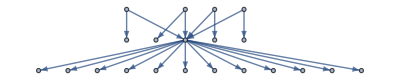

```mathematica
RelationsToEdges[1000]//Graph
```

```mathematica
Table[getAllVariables[newAssoc[key]["colofour"]],{key,Keys[newAssoc]}]//Tally//Sort
```

{{b01,1},{b02,1},{b03,1},{b04,1},{b05,1},{b06,1},{b07,1},{b08,1},{b09,1},{b10,1},{b11,1},{b12,1},{b13,1},{b14,1},{b15,1},{b16,1},{b17,1},{b18,1},{b19,1},{b20,1},{b21,1},{b22,1},{b23,1},{b24,1},{b25,1},{b26,1},{b27,1},{b28,1},{b29,1},{b30,1},{b31,1},{b32,1},{b33,1},{b34,1},{b35,1},{b36,1},{b37,1},{b38,1},{b39,1},{b40,1},{b41,1},{b42,1},{b43,1},{b44,1},{b45,1},{b46,1},{b47,1},{b48,1},{b49,1},{b50,1},{z,1},{{b01,b13},1},{{b01,b14},1},{{b01,b16},1},{{b02,b14},1},{{b02,b15},1},{{b02,b17},1},{{b03,b11},1},{{b03,b15},1},{{b03,b18},1},{{b04,b11},1},{{b04,b12},1},{{b04,b19},1},{{b05,b12},1},{{b05,b13},1},{{b05,b20},1},{{b06,b16},1},{{b06,b22},1},{{b06,b25},1},{{b07,b17},1},{{b07,b21},1},{{b07,b23},1},{{b08,b18},1},{{b08,b22},1},{{b08,b24},1},{{b09,b19},1},{{b09,b23},1},{{b09,b25},1},{{b10,b20},1},{{b10,b21},1},{{b10,b24},1},{{b26,b41},1},{{b27,b42},1},{{b28,b43},1},{{b29,b44},1},{{b30,b45},1},{{b31,b36},1},{{b32,b37},1},{{b33,b38},1},{{b34,b39},1},{{b35,b40},1},{{z,b01},1},{{z,b02},1},{{z,b03},1},{{z,b04},1},{{z,b05},1},{{z,b06},1},{{z,b07},1},{{z,b08},1},{{z,b09},1},{{z,b10},1},{{b01,b03,b07,b27},6},{{b01,b04,b10,b30},6},{{b01,b08,b09,b31},6},{{b02,b04,b08,b28},6},{{b02,b05,b06,b26},6},{{b02,b09,b10,b32},6},{{b03,b05,b09,b29},6},{{b03,b06,b10,b33},6},{{b04,b06,b07,b34},6},{{b05,b07,b08,b35},6},{{b11,b12,b19,b44},6},{{b11,b15,b18,b43},6},{{b11,b16,b21,b46},3},{{b11,z,b03,b04},1},{{b12,b13,b20,b45},6},{{b12,b17,b22,b47},3},{{b12,z,b04,b05},1},{{b13,b14,b16,b41},6},{{b13,b18,b23,b48},3},{{b13,z,b01,b05},1},{{b14,b15,b17,b42},6},{{b14,b19,b24,b49},3},{{b14,z,b01,b02},1},{{b15,b20,b25,b50},3},{{b15,z,b02,b03},1},{{b16,b22,b25,b36},6},{{b16,z,b01,b06},1},{{b17,b21,b23,b37},6},{{b17,z,b02,b07},1},{{b18,b22,b24,b38},6},{{b18,z,b03,b08},1},{{b19,b23,b25,b39},6},{{b19,z,b04,b09},1},{{b20,b21,b24,b40},6},{{b20,z,b05,b10},1},{{b21,z,b07,b10},1},{{b22,z,b06,b08},1},{{b23,z,b07,b09},1},{{b24,z,b08,b10},1},{{b25,z,b06,b09},1},{{b01,b13,b14,b16,b41},1},{{b02,b14,b15,b17,b42},1},{{b03,b11,b15,b18,b43},1},{{b04,b11,b12,b19,b44},1},{{b05,b12,b13,b20,b45},1},{{b06,b16,b22,b25,b36},1},{{b07,b17,b21,b23,b37},1},{{b08,b18,b22,b24,b38},1},{{b09,b19,b23,b25,b39},1},{{b10,b20,b21,b24,b40},1},{{z,b01,b03,b07,b27},1},{{z,b01,b04,b10,b30},1},{{z,b01,b08,b09,b31},1},{{z,b02,b04,b08,b28},1},{{z,b02,b05,b06,b26},1},{{z,b02,b09,b10,b32},1},{{z,b03,b05,b09,b29},1},{{z,b03,b06,b10,b33},1},{{z,b04,b06,b07,b34},1},{{z,b05,b07,b08,b35},1},{{b01,b03,b07,b14,b15,b17,b27,b42},6},{{b01,b04,b10,b12,b13,b20,b30,b45},6},{{b01,b08,b09,b16,b22,b25,b31,b36},6},{{b02,b04,b08,b11,b15,b18,b28,b43},6},{{b02,b05,b06,b13,b14,b16,b26,b41},6},{{b02,b09,b10,b17,b21,b23,b32,b37},6},{{b03,b05,b09,b11,b12,b19,b29,b44},6},{{b03,b06,b10,b18,b22,b24,b33,b38},6},{{b04,b06,b07,b19,b23,b25,b34,b39},6},{{b05,b07,b08,b20,b21,b24,b35,b40},6},{{z,b01,b02,b03,b07,b14,b15,b17,b27,b42},1},{{z,b01,b02,b05,b06,b13,b14,b16,b26,b41},1},{{z,b01,b04,b05,b10,b12,b13,b20,b30,b45},1},{{z,b01,b06,b08,b09,b16,b22,b25,b31,b36},1},{{z,b02,b03,b04,b08,b11,b15,b18,b28,b43},1},{{z,b02,b07,b09,b10,b17,b21,b23,b32,b37},1},{{z,b03,b04,b05,b09,b11,b12,b19,b29,b44},1},{{z,b03,b06,b08,b10,b18,b22,b24,b33,b38},1},{{z,b04,b06,b07,b09,b19,b23,b25,b34,b39},1},{{z,b05,b07,b08,b10,b20,b21,b24,b35,b40},1},{{b01,b02,b04,b08,b09,b10,b14,b19,b24,b28,b30,b31,b32,b49},65},{{b01,b03,b04,b06,b07,b10,b11,b16,b21,b27,b30,b33,b34,b46},65},{{b01,b03,b05,b07,b08,b09,b13,b18,b23,b27,b29,b31,b35,b48},65},{{b02,b03,b05,b06,b09,b10,b15,b20,b25,b26,b29,b32,b33,b50},65},{{b02,b04,b05,b06,b07,b08,b12,b17,b22,b26,b28,b34,b35,b47},65},{{z,b01,b02,b04,b08,b09,b10,b14,b19,b24,b28,b30,b31,b32,b49},1},{{z,b01,b03,b04,b06,b07,b10,b11,b16,b21,b27,b30,b33,b34,b46},1},{{z,b01,b03,b05,b07,b08,b09,b13,b18,b23,b27,b29,b31,b35,b48},1},{{z,b02,b03,b05,b06,b09,b10,b15,b20,b25,b26,b29,b32,b33,b50},1},{{z,b02,b04,b05,b06,b07,b08,b12,b17,b22,b26,b28,b34,b35,b47},1},{{b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45},12},{{b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},10},{{b01,b02,b04,b08,b09,b10,b14,b19,b24,b26,b27,b29,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},6},{{b01,b03,b04,b06,b07,b10,b11,b16,b21,b26,b28,b29,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},6},{{b01,b03,b05,b07,b08,b09,b13,b18,b23,b26,b28,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},6},{{b02,b03,b05,b06,b09,b10,b15,b20,b25,b27,b28,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},6},{{b02,b04,b05,b06,b07,b08,b12,b17,b22,b27,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},6},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b29,b32,b33,b37,b38,b41,b42,b43,b44,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b04,b07,b08,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b03,b04,b07,b08,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b30,b31,b32,b36,b37,b41,b42,b43,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b05,b06,b07,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b30,b31,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b03,b05,b06,b07,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b30,b31,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b32,b34,b35,b37,b39,b40,b41,b42,b43,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b07,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b29,b30,b31,b35,b36,b40,b41,b42,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b04,b05,b06,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b29,b30,b31,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b04,b05,b06,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b29,b30,b31,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b30,b31,b33,b34,b36,b38,b39,b41,b42,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b04,b05,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b28,b29,b30,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b28,b29,b30,b34,b35,b39,b40,b41,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b04,b05,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b28,b29,b30,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b03,b06,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b28,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b28,b31,b33,b34,b35,b36,b38,b39,b40,b41,b43,b46,b47,b48,b49,b50},2},{{b01,b03,b06,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b28,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b29,b30,b32,b33,b35,b37,b38,b40,b41,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b04,b05,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b04,b05,b07,b08,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b41,b44,b46,b47,b48,b49,b50},2},{{b01,b04,b06,b07,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b04,b06,b07,b08,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b02,b03,b04,b05,b08,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b27,b28,b29,b30,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b30,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b28,b29,b30,b33,b34,b38,b39,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b28,b29,b31,b33,b35,b36,b38,b40,b42,b43,b44,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b06,b08,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b03,b04,b06,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b27,b28,b29,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b29,b31,b32,b34,b35,b36,b37,b39,b40,b42,b44,b46,b47,b48,b49,b50},2},{{b02,b04,b06,b07,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b27,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b27,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b30,b32,b33,b34,b35,b37,b38,b39,b40,b42,b45,b46,b47,b48,b49,b50},2},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b28,b29,b30,b31,b32,b34,b36,b37,b39,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b03,b04,b05,b06,b07,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b28,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b03,b04,b05,b06,b07,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b28,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b28,b30,b31,b32,b33,b35,b36,b37,b38,b40,b43,b45,b46,b47,b48,b49,b50},2},{{b03,b05,b06,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b28,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b03,b05,b06,b07,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b28,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b03,b04,b07,b08,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b07,b08,b11,b13,b15,b16,b18,b20,b21,b23,b25,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b03,b04,b07,b08,b11,b13,b15,b16,b18,b20,b21,b23,b25,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b03,b04,b07,b08,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b07,b08,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b03,b04,b07,b08,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b30,b31,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b05,b06,b07,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b30,b31,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b05,b06,b07,b12,b14,b15,b17,b19,b20,b22,b24,b25,b27,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b03,b05,b06,b07,b12,b14,b15,b17,b19,b20,b22,b24,b25,b27,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b03,b07,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b03,b07,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b04,b05,b06,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b04,b05,b06,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b02,b04,b05,b06,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b29,b30,b31,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b04,b05,b06,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b29,b30,b31,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b04,b05,b06,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b04,b05,b06,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b05,b06,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b02,b05,b06,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b04,b05,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b28,b29,b30,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b04,b05,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b27,b28,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b03,b04,b05,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b27,b28,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b03,b04,b05,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b03,b04,b05,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b03,b04,b05,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b28,b29,b30,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b06,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b01,b03,b06,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b03,b06,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b28,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b06,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b28,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b06,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b27,b28,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b03,b06,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b27,b28,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b05,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b27,b28,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b27,b28,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b28,b29,b30,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b28,b29,b30,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b06,b07,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b28,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b28,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b06,b07,b08,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b06,b07,b08,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b27,b28,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b01,b04,b06,b07,b08,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b27,b28,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b27,b28,b29,b30,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b04,b05,b08,b09,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b02,b03,b04,b05,b08,b09,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b30,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b04,b06,b08,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b02,b03,b04,b06,b08,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b03,b04,b06,b08,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b04,b06,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b02,b03,b04,b06,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b02,b03,b04,b06,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b27,b28,b29,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b04,b06,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b04,b06,b07,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b28,b29,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b02,b04,b06,b07,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b28,b29,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b02,b04,b06,b07,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b27,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b05,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b29,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b29,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b05,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b28,b29,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b02,b05,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b28,b29,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b27,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b04,b05,b06,b07,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b27,b28,b29,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b03,b04,b05,b06,b07,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b27,b28,b29,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b03,b04,b05,b06,b07,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b28,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b04,b05,b06,b07,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b27,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b03,b04,b05,b06,b07,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b27,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b03,b04,b05,b06,b07,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b28,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b05,b06,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b27,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49},1},{{b03,b05,b06,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b27,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b28,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b05,b06,b07,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b27,b28,b29,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b27,b28,b29,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b28,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b06,b09,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b01,b02,b03,b04,b06,b09,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b01,b02,b03,b04,b06,b09,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b02,b03,b04,b06,b09,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b01,b02,b03,b04,b06,b09,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b01,b02,b03,b04,b06,b09,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b29,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b02,b03,b05,b08,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b01,b02,b03,b05,b08,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b01,b02,b03,b05,b08,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b02,b03,b05,b08,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b01,b02,b03,b05,b08,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b01,b02,b03,b05,b08,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b02,b04,b05,b07,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b02,b04,b05,b07,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b04,b05,b07,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b01,b02,b04,b05,b07,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b02,b04,b05,b07,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b04,b05,b07,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b02,b06,b07,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b01,b05,b06,b07,b09,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b01,b05,b06,b07,b09,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b01,b05,b06,b07,b09,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b05,b06,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b01,b05,b06,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b01,b05,b06,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b02,b03,b04,b05,b07,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b02,b03,b06,b07,b08,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b02,b03,b06,b07,b08,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b02,b03,b06,b07,b08,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b02,b03,b06,b07,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b02,b03,b06,b07,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b02,b03,b06,b07,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b03,b04,b07,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b04,b05,b06,b08,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b04,b05,b06,b08,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b04,b05,b06,b08,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b04,b05,b06,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b04,b05,b06,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b04,b05,b06,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b28,b29,b30,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b30,b31,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b28,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b29,b30,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b29,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b02,b03,b04,b07,b08,b11,b13,b15,b16,b18,b20,b21,b23,b25,b27,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b04,b07,b08,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b27,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b01,b02,b03,b05,b06,b07,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b05,b06,b07,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b27,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b29,b30,b31,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},1},{{b01,b02,b03,b07,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b01,b02,b04,b05,b06,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b04,b05,b06,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b29,b30,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b30,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},1},{{b01,b03,b04,b05,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b27,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b28,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b03,b04,b05,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b03,b06,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b28,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b03,b06,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b27,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b29,b30,b31,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},1},{{b01,b04,b05,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b27,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b04,b05,b07,b08,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b28,b29,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},1},{{b01,b04,b06,b07,b08,b09,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b28,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b04,b06,b07,b08,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b27,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b29,b30,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},1},{{b02,b03,b04,b06,b08,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b03,b04,b06,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b29,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b02,b04,b06,b07,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b30,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},1},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b30,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},1},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},1},{{b03,b04,b05,b06,b07,b09,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b27,b28,b29,b30,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b03,b04,b05,b06,b07,b09,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b27,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b30,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},1},{{b03,b05,b06,b07,b08,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b27,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b03,b05,b06,b07,b08,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b27,b28,b29,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b11,b12,b13,b16,b17,b18,b22,b23,b26,b27,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b12,b13,b14,b17,b18,b19,b22,b23,b26,b27,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b12,b13,b15,b17,b18,b22,b23,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b10,b11,b12,b13,b16,b17,b18,b21,b22,b26,b27,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b10,b11,b12,b14,b16,b17,b21,b22,b24,b26,b27,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b10,b11,b12,b15,b16,b17,b20,b21,b22,b26,b27,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b48,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b09,b10,b11,b12,b15,b16,b17,b20,b21,b25,b26,b27,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},2},{{b01,b02,b03,b04,b05,b06,b07,b09,b10,b11,b13,b15,b16,b20,b21,b23,b25,b26,b27,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},2},{{b01,b02,b03,b04,b05,b06,b07,b09,b10,b11,b14,b15,b16,b19,b20,b21,b25,b26,b27,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b49},2},{{b01,b02,b03,b04,b05,b06,b08,b09,b10,b11,b14,b15,b16,b19,b20,b24,b25,b26,b27,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},2},{{b01,b02,b03,b04,b05,b06,b08,b09,b10,b12,b14,b15,b19,b20,b22,b24,b25,b26,b27,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},2},{{b01,b02,b03,b04,b05,b06,b08,b09,b10,b13,b14,b15,b18,b19,b20,b24,b25,b26,b27,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48},2},{{b01,b02,b03,b04,b05,b07,b08,b09,b10,b11,b13,b14,b18,b19,b21,b23,b24,b26,b27,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},2},{{b01,b02,b03,b04,b05,b07,b08,b09,b10,b12,b13,b14,b17,b18,b19,b23,b24,b26,b27,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},2},{{b01,b02,b03,b04,b05,b07,b08,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b26,b27,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b50},2},{{b01,b02,b03,b04,b06,b07,b08,b09,b10,b11,b14,b15,b16,b19,b21,b24,b25,b26,b27,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},2},{{b01,b02,b03,b04,b06,b07,b08,b09,b10,b11,b14,b16,b17,b19,b21,b22,b24,b26,b27,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},2},{{b01,b02,b03,b04,b06,b07,b08,b09,b10,b11,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b48,b50},2},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b29,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b05,b06,b07,b08,b09,b10,b13,b14,b15,b18,b20,b23,b24,b25,b26,b27,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},2},{{b01,b02,b03,b05,b06,b07,b08,b09,b10,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},2},{{b01,b02,b03,b05,b06,b07,b08,b09,b10,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b49},2},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b30,b31,b32,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b04,b05,b06,b07,b08,b09,b10,b12,b13,b14,b17,b19,b22,b23,b24,b26,b27,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},2},{{b01,b02,b04,b05,b06,b07,b08,b09,b10,b12,b14,b16,b17,b19,b21,b22,b24,b26,b27,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},2},{{b01,b02,b04,b05,b06,b07,b08,b09,b10,b12,b14,b17,b19,b20,b22,b24,b25,b26,b27,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b50},2},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b29,b30,b31,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b04,b08,b09,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b30,b31,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b16,b18,b21,b22,b23,b26,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},2},{{b01,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b16,b18,b19,b21,b23,b24,b26,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},2},{{b01,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b16,b18,b20,b21,b23,b25,b26,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b47,b49,b50},2},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b28,b29,b30,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b03,b04,b06,b07,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b03,b05,b07,b08,b09,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b28,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b29,b30,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b29,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b15,b17,b20,b21,b22,b25,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},2},{{b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b15,b17,b18,b20,b22,b23,b25,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},2},{{b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b15,b17,b19,b20,b22,b24,b25,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b48,b49},2},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b28,b29,b30,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b28,b29,b31,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b03,b05,b06,b09,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b04,b05,b06,b07,b08,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b27,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b27,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b28,b29,b30,b31,b32,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b28,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b06,b09,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b03,b04,b06,b09,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b03,b05,b08,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b03,b05,b08,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b04,b05,b07,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b04,b05,b07,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b06,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b29,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b06,b07,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b29,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b03,b04,b05,b06,b08,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b05,b06,b07,b09,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b05,b06,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b28,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b03,b04,b05,b07,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b03,b04,b05,b07,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b03,b06,b07,b08,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b30,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b02,b03,b06,b07,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b30,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b03,b04,b07,b08,b09,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b03,b04,b07,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b04,b05,b06,b08,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b04,b05,b06,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},3},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b04,b07,b08,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b05,b06,b07,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b07,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b04,b05,b06,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b05,b06,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b04,b05,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b26,b27,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b03,b06,b08,b09,b10,b11,b13,b14,b15,b16,b18,b19,b20,b21,b23,b24,b25,b27,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b29,b30,b31,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b04,b05,b07,b08,b10,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b26,b27,b28,b30,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b04,b06,b07,b08,b09,b11,b12,b13,b14,b16,b17,b18,b19,b21,b22,b23,b24,b27,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b05,b08,b09,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b30,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b29,b30,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b03,b04,b06,b08,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b27,b28,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b04,b06,b07,b09,b10,b11,b12,b14,b15,b16,b17,b19,b20,b21,b22,b24,b25,b26,b28,b29,b30,b31,b32,b33,b34,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b27,b28,b29,b31,b32,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b02,b05,b07,b08,b09,b10,b12,b13,b14,b15,b17,b18,b19,b20,b22,b23,b24,b25,b26,b28,b29,b30,b31,b32,b33,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b30,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b03,b04,b05,b06,b07,b09,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b28,b29,b31,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b03,b05,b06,b07,b08,b10,b11,b12,b13,b15,b16,b17,b18,b20,b21,b22,b23,b25,b26,b27,b29,b30,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},2},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b16,b17,b18,b21,b22,b23,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b14,b16,b17,b19,b21,b22,b24,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b15,b16,b17,b20,b21,b22,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b14,b16,b18,b19,b21,b23,b24,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b13,b15,b16,b18,b20,b21,b23,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b14,b15,b16,b19,b20,b21,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b13,b14,b17,b18,b19,b22,b23,b24,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b13,b15,b17,b18,b20,b22,b23,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b12,b14,b15,b17,b19,b20,b22,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b13,b14,b15,b18,b19,b20,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},4},{{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},475},{{z,b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50},1}}

```mathematica
Length[{b01,b02,b03,b04,b05,b06,b07,b08,b09,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48,b49,b50}]
```

50